{a→0.988652,c→-42.7931}

Function[{r},-2.74828 ⅇ^(-0.511544 r^2)-Erf[0.715223 r]/r]

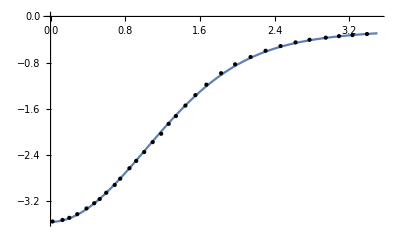

```mathematica
data=Import["C:\\Users\\ASUS\\Documents\\Lepage_VeLO.dat","CSV"];
(*data={{0.021390374331550777,-3.548192771084337},{0.12834224598930488,-3.5210843373493974},{0.2005347593582889,-3.484939759036144},{0.2860962566844921,-3.4216867469879517},{0.38502673796791453,-3.322289156626505},{0.4679144385026738,-3.2319277108433733},{0.5267379679144384,-3.1596385542168672},{0.5962566844919786,-3.0512048192771077},{0.6871657754010694,-2.9156626506024086},{0.7459893048128341,-2.80722891566265},{0.8449197860962565,-2.6265060240963853},{0.9171122994652405,-2.5},{1.0026737967914439,-2.346385542168674},{1.093582887700535,-2.1746987951807224},{1.1844919786096257,-2.0301204819277108},{1.2647058823529413,-1.8584337349397586},{1.3422459893048129,-1.72289156626506},{1.4438502673796787,-1.5421686746987944},{1.550802139037433,-1.3614457831325297},{1.668449197860962,-1.1807228915662646},{1.82620320855615,-0.9819277108433733},{1.9759358288770053,-0.8283132530120483},{2.141711229946524,-0.701807228915662},{2.3021390374331547,-0.593373493975903},{2.4625668449197855,-0.5120481927710836},{2.622994652406417,-0.4487951807228914},{2.7727272727272725,-0.403614457831325},{2.946524064171123,-0.367469879518072},{3.0882352941176467,-0.3403614457831319},{3.232620320855615,-0.3222891566265056},{3.3877005347593583,-0.30421686746987886}}*)
α=1;
model:=-α/r Erf[r/(√2 a)]+c  a^2 (E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3)(*DiracDelta[r]*)
fit=FindFit[data,model,{a,c},r]
modelf=Function[{r},Evaluate[model/.fit]]
Plot[modelf[r],{r,0,3.5},Epilog->Map[Point,data]]
```